# Trapped-Ions Oxford/Hub virtual device

Set environment, such as threads, gpu, etc.

```mathematica
SetEnvironment["OMP_NUM_THREADS"->"8"]
SetDirectory[NotebookDirectory[]];
```

Load the QuESTLink

```mathematica
Import["/home/cica/programs/QuESTlink/Link/QuESTlink.m"];
CreateLocalQuESTEnv["quest_link_cpu"];
```

Virtual quantum devices, loaded after questlink

```mathematica
Get["../vqd.wl"]
```

Time unit : μs
Frequency unit: MHz

Interesting thing to put in paper:
The total time
Time profile
Bottleneck: dominant contribution of noise

```mathematica
Options[TrappedIonOxford]={
(*the nodes name together with the total qubits on each node*)
Nodes-><|"Alice"->4,"Bob"->4|>,
(* time and duration unit μs: 3000 s*)
T1-><|"Alice"->3*10^9, "Bob"->3*10^9    |>,
(* Simulating T2* error by gaussian decay: 10 ms *)
T2s-><|"Alice"->10^5,  "Bob"->10^5   |>,
(* Switch on/off the standard passive noise: Amplitude damping T1 and dephasing T2  *)
StdPassiveNoise->True,
(* Duration for moving operations: Split, Combine, and physical swap; they have zero error *)
DurMove-><|
"Alice"-> <|Shutl->25, Splz->50, Comb->50, SWAPLoc->10 |>,
"Bob"-><|Shutl->25, Splz->50, Comb->50, SWAPLoc->10 |>
|>,
(* fidelity of preparation/initialisation; initialisation is done by amplitude damping *)
FidInit-><|"Alice"->0.9999, "Bob"->0.9998|>,
DurInit-><|"Alice"->20,"Bob"->20|>,

(* Readout error includes bitflip and scattering
Bitflip error represents symmetric error on both 0 and 1 readout  
Amplitude damping (change to depol) represents scattering error affecting the neighborhood qubits (in the same zone): collapsing the superposition into 0
*)
DurRead-><|"Alice"->50, "Bob"->50|>,
BFProb-><|"Alice"->10^-3,"Bob"->10^-3|>,
(* delete this *)
ScatProb-><|"Alice"->0.05, "Bob"->0.05|>,

(*Fidelity of single x- and y- rotations; z-rotation is instaneous (noiseless, virtual)
future:Set manually the error coefficient instead of setting the fidelity at the first place.
Future: off-resonant oscillation in the same zone*)
FidSingleXY-><|"Alice"->0.99999, "Bob"->0.99999|>,
(*fraction of depolarising:dephasing noise of the x- and y- rotations *)
EFSingleXY-><|"Alice"->{1,0},"Bob"->{1,0}|>,

(* Frequency unit is MHz *)
(* Rabi frequency on single rotations in MHz  *)
RabiFreq-><|"Alice"->10, "Bob"->10 |>,
(* Frequency of CZ operation*)
FreqCZ-><|"Alice"->0.1,"Bob"->0.1|>,
(*Fidelity of controlled-Z operation *)
FidCZ-><|"Alice"->0.999, "Bob"->0.999|>,
(* add a bit of bit-flip: small fraction of population is depolarised *)
EFCZ-><|"Alice"->{0.1,0.9},"Bob"->{0.1,0.9}|>,
(* frequency of remote entanglement MHz
initial state also heralded entanglement.
 *)
FreqEnt->0.1,
(* fidelity of remote entanglement *)
FidEnt->0.95,
(* fraction of noise: depolarizing:dephasing *)
EFEnt->{0.1,0.9}
};
```

[Native Gates]
 Init_q[node], Read_q[node], Rx_q[node,θ], Ry_q[node,θ], CZ_(q1,q2)[node], Ent[node1, node2], SWAPLoc_(q1,q2)[node], Splz_(q1,q2)[node,zone_destination], Comb_(q1,q2)[node], Comb_(q1,q2)[node,zone_destination]
[Zone and operations]
[from notes]
Zone 1 : prepare, store?, detect
Zone 2 : prepare, store?, detect, logic
Zone 3 : prepare, store?, detect, logic
Zone 4 : remote entangle
[from email]
    a. Zone 1 supports prep, detect, split, combine and rotate (SWAP), but
        no local or remote quantum logic
     b. Zone 2 and 3 are as (a) plus local logic (1Q and 2Q) 
     c. Zone 4 supports remote logic only (no split, no combine, only shuttle for the move)

Basic remote entanglement from the note. The total circuit and moves until page 38. The expected result is qubit 4 at zone 2 is highly entangled after 3 distillations .

```mathematica
(* Transformation to the Bell basis *)
mat2BellBasis[m_]:=With[
{p=(1/√2)*{{1,1,0,0},{0,0,1,-1},{0,0,1,1},{1,-1,0,0}},
pinv=(1/√2)*{{1,0,0,1},{1,0,0,-1},{0,1,1,0},{0,-1,1,0}}},
pinv.m.p]
```

```mathematica
chartbell[label_]:={ImageSize->200,BarSpacing->0.1,ColorFunction->Function[{height},getcolor[height]],ChartElementFunction->"Cube",ChartStyle->EdgeForm[Thick],PlotTheme->"Business",Ticks->{{{1,"Φ+"},{2,"Φ-"},{3,"Ψ+"},{4,"Ψ-"}},{{1,"Φ+"},{2,"Φ-"},{3,"Ψ+"},{4,"Ψ-"}},Automatic},LabelStyle->Directive[Bold,FontFamily->"Helvetica"],
Epilog->Inset[Style[label,17,Bold],ImageScaled[{.3,.9}]],PlotRange->{{0.5,4.5},{0.5,4.5},{0,1}},
LabelingFunction->(Placed[Rotate[
Which[
#>=0.5,Style[NumberForm[#,5],13,GrayLevel[0.82]],
(#>=0.001)&&(#<0.5),Style[NumberForm[#,2],10,Black],
True,Style[ScientificForm[#,2],10,Black]
]
,90 Degree],If[#1>=0.5,Center,Above]]&),
ViewAngle->All,
FaceGrids->None,
BoxRatios->{1,1,0.5},Axes->{True,True,False}
};
getcolor[height_]:=(If[height<=0.5,ColorData["IslandColors"][1+0.1Log10@height],ColorData["RedBlueTones"][height]])
```

```mathematica
circ={Subscript[Splz, 2,3]["Alice",3],Subscript[Splz, 2,3]["Bob",3],Subscript[Init, 3]["Alice"],Subscript[Init, 4]["Alice"],Subscript[Init, 3]["Bob"],Subscript[Init, 4]["Bob"],Subscript[Splz, 3,4]["Alice",4],Subscript[Splz, 3,4]["Bob",4],Subscript[Ent, 4,4]["Alice","Bob"],Subscript[Comb, 3,4]["Alice",3],Subscript[Comb, 3,4]["Bob",3],Subscript[SWAPLoc, 3,4]["Alice"],Subscript[SWAPLoc, 3,4]["Bob"],Subscript[Splz, 4,3]["Alice",4],Subscript[Splz, 4,3]["Bob",4],Subscript[Ent, 3,3]["Alice","Bob"],Subscript[Comb, 4,3]["Alice",3],Subscript[Comb, 4,3]["Bob",3],Subscript[CZ, 4,3]["Alice"],Subscript[CZ, 4,3]["Bob"],Subscript[Splz, 4,3]["Alice",2],Subscript[Splz, 4,3]["Bob",2],Subscript[Init, 1]["Alice"],Subscript[Init, 1]["Bob"],Subscript[Read, 3]["Alice"],Subscript[Read, 3]["Bob"],Subscript[Splz, 1,2]["Alice",2],Subscript[Splz, 1,2]["Bob",2],Subscript[Init, 3]["Alice"],Subscript[Init, 3]["Bob"],Subscript[Comb, 2,4]["Alice"],Subscript[Comb, 2,4]["Bob"],Subscript[Shutl, 3]["Alice",4],Subscript[Shutl, 3]["Bob",4],Subscript[Ent, 3,3]["Alice","Bob"],Subscript[SWAPLoc, 2,4]["Alice"],Subscript[SWAPLoc, 2,4]["Bob"],Subscript[Splz, 4,2]["Alice",3],Subscript[Splz, 4,2]["Bob",3],Subscript[Comb, 2,3]["Alice",3],Subscript[Comb, 2,3]["Bob",3],Subscript[SWAPLoc, 2,3]["Alice"],Subscript[SWAPLoc, 2,3]["Bob"],Subscript[Splz, 3,2]["Alice",4],Subscript[Splz, 3,2]["Bob",4],
Subscript[Ent, 2,2]["Alice","Bob"],Subscript[Comb, 3,2]["Alice",3],Subscript[Comb, 3,2]["Bob",3],Subscript[CZ, 3,2]["Alice"],Subscript[CZ, 3,2]["Bob"],Subscript[Splz, 3,2]["Alice",2],Subscript[Splz, 3,2]["Bob",2],Subscript[Comb, 4,3]["Alice"],Subscript[CZ, 4,3]["Alice"],Subscript[Comb, 4,3]["Bob"],Subscript[CZ, 4,3]["Bob"],Subscript[Read, 2]["Alice"],Subscript[Read, 2]["Bob"],Subscript[H, 4]["Alice"],Subscript[H, 3]["Alice"],Subscript[H, 3]["Bob"],Subscript[H, 4]["Bob"],Subscript[CZ, 4,3]["Alice"],Subscript[CZ, 4,3]["Bob"],Subscript[Shutl, 2]["Alice",4],Subscript[Shutl, 2]["Bob",4],Subscript[Splz, 4,3]["Alice",3],Subscript[Splz, 4,3]["Bob",3]
}/.{Subscript[H, q_][n_]:>Subscript[Rx, q][n,π/2]};
```

Check the arrangement of the circuit in the total density matrix. Here is completely serial within a node.
 It does not update the device state, thus we cannot check the final position of ions.

```mathematica
(*DrawCircuit@CircTrappedIons[circ,dev]*)
```

This will show the total scheduling, noise operation, and the final form in the simulation.
Set the MapQubits->False and ReplaceAliases->True if you intended to do the density matrix simulation

```mathematica
dev=TrappedIonOxford[];
circ2=CircTrappedIons[circ,dev,MapQubits->False];
noisycirc=InsertCircuitNoise[circ2,dev, ReplaceAliases->True];
(*DrawCircuit[%,8]*)
```

```mathematica
DestroyAllQuregs[];
ρ=CreateDensityQureg[8];
```

```mathematica
ApplyCircuit[ρ,ExtractCircuit@noisycirc];
PlotDensityMatrix[mat2BellBasis@PartialTrace[ρ,0,1,2,4,5,6],Sequence@@chartbell[""]]
```

-Graphics3D-

Recall the expected result is qubit 4 at zone 2 is highly entangled after 3 distillations: trace out the rest except qubit 4 at both nodes. Thus we trace out the rest of other qubits above.

```mathematica
dev@ShowNodes
```

Alice | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Bob | -Graphics- | -Graphics- | -Graphics- | -Graphics-

[FUTURE FEATURES]
T1, and T2 for individual qubits
T1-><|”Alice”-><|1->100,2->101|>, “Bob”->110 |>,
ModifyDev[dev,Opts->xxx]. One can modify T1, T2 in between.
Passive noise different on each zone.
Correlated noise happens only to qubits with the same zone.
Measurement involves scattering that can affect neighborhood atoms within radius.
Parrallel -> False (done), Default (no operations in the same zone, always parallel Alice and Bob, Ent is always serial) , Full (Default+ parallel when in different zone)

## Distillations on 3- and 4-ions on each node for up to 3 rounds sequence: 0 = dephasing distillation; 1=bitflip distillation

```mathematica
(* Bit-Flip distillation operation: The CNOT equivalent *)
cx={Subscript[Ry, 1][-π/2],Subscript[C, 0][Subscript[Z, 1]],Subscript[Ry, 1][π/2]};
(* Phase-flip distillation: Alice and Bob *)
pfa={Subscript[Ry, 0][-π/2],Subscript[C, 0][Subscript[Z, 1]],Subscript[Rx, 1][π],Subscript[Ry, 1][-π/2]};
pfb={Subscript[Ry, 0][π/2],Subscript[C, 0][Subscript[Z, 1]],Subscript[Ry, 1][π/2]};
```

```mathematica
heraldout::usage="heraldout[outputs]. Check if all outputs 00 or 11 in all measurement outcomes.";
heraldout[out_]:=With[{fout=Flatten@out},If[Length@fout>1,And@@(Equal@@@Partition[fout,2]),True]]
```

```mathematica
distcirc[p_,q_]:=<|
(*dephasing distillation sequence*)
0->Sequence@@{Subscript[Ry, p]["Alice",π/2],Subscript[Ry, p]["Bob",π/2],Subscript[CZ, p,q]["Alice"],Subscript[CZ, p,q]["Bob"],Subscript[Ry, q]["Alice",π/2],Subscript[Rx, p]["Alice",π],Subscript[Ry, q]["Bob",π/2]},
(*bitflip distillation sequence*)
1->Sequence@@{Subscript[Ry, q]["Alice",-π/2],Subscript[Ry, q]["Bob",-π/2],Subscript[CZ, p,q]["Alice"],Subscript[CZ, p,q]["Bob"],Subscript[Ry, q]["Alice",π/2],Subscript[Ry, q]["Bob",π/2]}
|>;

(* 3 ions on each nodes, up to 2 rounds of distillation*)
DistCircTrappedIons3::usage="DistillationOnTrappedIons3[sequence]. Distillation on 3-ions of two nodes. Works up to 2 rounds. Sequence contains 0 (dephasing) or 1 (bit-flip). Qubit 3 is always the final qubit.";
DistCircTrappedIons3[sequence_:{}]:=Module[{circ,nrounds},
(* raw entangled pairs *)
nrounds=Length@sequence;
circ={Subscript[Splz, 2,3]["Alice",4],Subscript[Splz, 2,3]["Bob",4],Subscript[Ent, 3,3]["Alice","Bob"]};
If[nrounds>=1,
circ=Join[circ,{Subscript[Splz, 1,2]["Alice",2],Subscript[Splz, 1,2]["Bob",2],Subscript[Comb, 2,3]["Alice",2],Subscript[Comb, 2,3]["Bob",2],Subscript[SWAPLoc, 2,3]["Alice"],Subscript[SWAPLoc, 2,3]["Bob"],Subscript[Splz, 3,2]["Alice",4],Subscript[Splz, 3,2]["Bob",4],Subscript[Ent, 2,2]["Alice","Bob"],Subscript[Comb, 3,2]["Alice",2],Subscript[Comb, 3,2]["Bob",2],distcirc[3,2][sequence[[1]]],Subscript[Splz, 3,2]["Alice",3],Subscript[Splz, 3,2]["Bob",3],Subscript[Read, 2]["Alice"],Subscript[Read, 2]["Bob"]}]];
If[nrounds>=2,
circ=Join[circ,{Subscript[Shutl, 2]["Alice",4],Subscript[Shutl, 2]["Bob",4],Subscript[Ent, 2,2]["Alice","Bob"],Subscript[Comb, 1,3]["Alice",1],Subscript[Comb, 1,3]["Bob",1],Subscript[SWAPLoc, 1,3]["Alice"],Subscript[SWAPLoc, 1,3]["Bob"],Subscript[Splz, 3,1]["Alice",3],Subscript[Splz, 3,1]["Bob",3],Subscript[Comb, 1,2]["Alice",3],Subscript[Comb, 1,2]["Bob",3],
Subscript[SWAPLoc, 1,2]["Alice"],Subscript[SWAPLoc, 1,2]["Bob"],Subscript[Splz, 2,1]["Alice",4],Subscript[Splz, 2,1]["Bob",4],Subscript[Ent, 1,1]["Alice","Bob"],Subscript[Comb, 2,1]["Alice",3],Subscript[Comb, 2,1]["Bob",3],
distcirc[2,1][sequence[[1]]],Subscript[Splz, 2,1]["Alice",2],Subscript[Splz, 2,1]["Bob",2],Subscript[Read, 1]["Alice"],Subscript[Read, 1]["Bob"],Subscript[Comb, 3,2]["Alice",2],Subscript[Comb, 3,2]["Bob",2],distcirc[3,2][sequence[[2]]],Subscript[Splz, 3,2]["Alice",1],Subscript[Splz, 3,2]["Bob",1],Subscript[Read, 2]["Alice"],Subscript[Read, 2]["Bob"]}]];
circ
]
(* 4 ions on each nodes, up to 3 rounds of distillation*)
DistCircTrappedIons4::usage="DistillationOnTrappedIons4[sequence]. Distillation on 4-ions of two nodes. Works up to 3 rounds. Sequence contains 0 (dephasing) or 1 (bit-flip). Qubit 4 is always the final qubit.";
DistCircTrappedIons4[sequence_:{}]:=Module[{circ,nrounds},
nrounds=Length@sequence;
(* raw entangled pairs *)
circ={Subscript[Splz, 3,4]["Alice",4],Subscript[Splz, 3,4]["Bob",4],Subscript[Ent, 4,4]["Alice","Bob"]};
If[nrounds>=1,
circ=Join[circ,{Subscript[Splz, 2,3]["Alice",3],Subscript[Splz, 2,3]["Bob",3],Subscript[Comb, 3,4]["Alice",3],Subscript[Comb, 3,4]["Bob",3],Subscript[SWAPLoc, 3,4]["Alice"],Subscript[SWAPLoc, 3,4]["Bob"],Subscript[Splz, 4,3]["Alice",4],Subscript[Splz, 4,3]["Bob",4],Subscript[Ent, 3,3]["Alice","Bob"],Subscript[Comb, 4,3]["Alice",3],Subscript[Comb, 4,3]["Bob",3],distcirc[4,3][sequence[[1]]],Subscript[Splz, 4,3]["Alice",2],Subscript[Splz, 4,3]["Bob",2],Subscript[Read, 3]["Alice"],Subscript[Read, 3]["Bob"]}]];
If[nrounds>=2,
circ=Join[circ,{Subscript[Shutl, 3]["Alice",4],Subscript[Shutl, 3]["Bob",4],Subscript[Ent, 3,3]["Alice","Bob"],Subscript[Splz, 1,2]["Alice",2],Subscript[Splz, 1,2]["Bob",2],Subscript[Comb, 2,4]["Alice",2],Subscript[Comb, 2,4]["Bob",2],Subscript[SWAPLoc, 2,4]["Alice"],Subscript[SWAPLoc, 2,4]["Bob"],Subscript[Comb, 2,3]["Alice",2],Subscript[Comb, 2,3]["Bob",2],Subscript[SWAPLoc, 2,3]["Alice"],Subscript[SWAPLoc, 2,3]["Bob"],Subscript[Splz, 4,3]["Alice",3],Subscript[Splz, 4,3]["Bob",3],Subscript[Splz, 3,2]["Alice",4],Subscript[Splz, 3,2]["Bob",4],Subscript[Ent, 2,2]["Alice","Bob"],Subscript[Comb, 3,2]["Alice",3],Subscript[Comb, 3,2]["Bob",3],distcirc[3,2][sequence[[1]]],Subscript[Splz, 3,2]["Alice",2],Subscript[Splz, 3,2]["Bob",2],Subscript[Read, 2]["Alice"],Subscript[Read, 2]["Bob"],Subscript[Comb, 4,3]["Alice"],Subscript[Comb, 4,3]["Bob"],distcirc[4,3][sequence[[2]]],Subscript[Splz, 4,3]["Alice",1],Subscript[Splz, 4,3]["Bob",1],Subscript[Read, 3]["Alice"],Subscript[Read, 3]["Bob"]}]];
If[nrounds>=3,
circ=Join[circ,{Subscript[Comb, 1,4]["Alice"],Subscript[Comb, 1,4]["Bob"],Subscript[SWAPLoc, 1,4]["Alice"],Subscript[SWAPLoc, 1,4]["Bob"],Subscript[Shutl, 2]["Alice",4],Subscript[Shutl, 2]["Bob",4],Subscript[Ent, 2,2]["Alice","Bob"],Subscript[Comb, 3,2]["Alice",2],Subscript[Comb, 3,2]["Bob",2],Subscript[SWAPLoc, 3,2]["Alice"],Subscript[SWAPLoc, 3,2]["Bob"],Subscript[Splz, 2,3]["Alice",4],Subscript[Splz, 2,3]["Bob",4],Subscript[Ent, 3,3]["Alice","Bob"],Subscript[Comb, 2,3]["Alice",2],Subscript[Comb, 2,3]["Bob",2],distcirc[2,3][sequence[[1]]],Subscript[Splz, 2,3]["Alice",3],Subscript[Splz, 2,3]["Bob",3],Subscript[Read, 3]["Alice"],Subscript[Read, 3]["Bob"],Subscript[Shutl, 3]["Alice",4],Subscript[Shutl, 3]["Bob",4],Subscript[Ent, 3,3]["Alice","Bob"],Subscript[Splz, 4,1]["Alice",2],Subscript[Splz, 4,1]["Bob",2],Subscript[Comb, 1,2]["Alice"],Subscript[Comb, 1,2]["Bob"],Subscript[SWAPLoc, 1,2]["Alice"],Subscript[SWAPLoc, 1,2]["Bob"],Subscript[Splz, 2,1]["Alice",3],Subscript[Splz, 2,1]["Bob",3],Subscript[Comb, 1,3]["Alice",3],Subscript[Comb, 1,3]["Bob",3],Subscript[SWAPLoc, 1,3]["Alice"],Subscript[SWAPLoc, 1,3]["Bob"],Subscript[Splz, 3,1]["Alice",4],Subscript[Splz, 3,1]["Bob",4],Subscript[Ent, 1,1]["Alice","Bob"],Subscript[Comb, 3,1]["Alice",3],Subscript[Comb, 3,1]["Bob",3],distcirc[3,1][sequence[[1]]],Subscript[Splz, 3,1]["Alice",2],Subscript[Splz, 3,1]["Bob",2],Subscript[Read, 1]["Alice"],Subscript[Read, 1]["Bob"],Subscript[Comb, 2,3]["Alice"],Subscript[Comb, 2,3]["Bob"],distcirc[2,3][sequence[[2]]],Subscript[Splz, 2,3]["Alice",1],Subscript[Splz, 2,3]["Bob",1],Subscript[Read, 3]["Alice"],Subscript[Read, 3]["Bob"],Subscript[Shutl, 3]["Alice",3],Subscript[Shutl, 3]["Bob",3],Subscript[Comb, 4,2]["Alice"],Subscript[Comb, 4,2]["Bob"],Subscript[Shutl, 4,2]["Alice",2],Subscript[Shutl, 4,2]["Bob",2],distcirc[4,2][sequence[[3]]],Subscript[Splz, 4,2]["Alice",1],Subscript[Splz, 4,2]["Bob",1],Subscript[Read, 2]["Alice"],Subscript[Read, 2]["Bob"]}]];
(*add random wait to see the full timing*)
circ=Join[circ,{Subscript[Wait, 0]["Alice",1],Subscript[Wait, 0]["Bob",1]}];
circ
];
```

### Play around with the parameters

```mathematica
chartbell[label_]:={ImageSize->200,BarSpacing->0.1,ColorFunction->Function[{height},getcolor[height]],ChartElementFunction->"Cube",ChartStyle->EdgeForm[Thick],PlotTheme->"Business",Ticks->{{{1,"Φ+"},{2,"Φ-"},{3,"Ψ+"},{4,"Ψ-"}},{{1,"Φ+"},{2,"Φ-"},{3,"Ψ+"},{4,"Ψ-"}},Automatic},LabelStyle->Directive[Bold,FontFamily->"Serif"],
Epilog->Inset[Style[label,16,Bold,FontFamily->"Serif"],ImageScaled[{.3,.9}]],PlotRange->{{0.5,4.5},{0.5,4.5},{0,1}},
LabelingFunction->(Placed[Rotate[
Which[
#>=0.5,Style[NumberForm[#,5],13,GrayLevel[0.82]],
(#>=0.001)&&(#<0.5),Style[NumberForm[#,2],10,Black],
True,Style[ScientificForm[#,2],10,Black]
]
,90 Degree],If[#1>=0.5,Center,Above]]&),
ViewAngle->All,
FaceGrids->None,
BoxRatios->{1,1,0.6},Axes->{True,True,False}
};
```

```mathematica
TIonDist::usage="TIonDist[ρ,sequence:{},device_option:{}]. Distillation simulation on trapped ions.";
TIonDist[ρ_,sequence_:{},devoptions_:{}]:=Module[
{dev,circ,noisysch,noisycirc,nions},
dev=TrappedIonOxford[Sequence@@devoptions];
nions=Min[Length/@Flatten/@Values@Values@dev[Nodes]];
circ=If[nions<=3,
DistCircTrappedIons3[sequence],
DistCircTrappedIons4[sequence]
];
noisysch=InsertCircuitNoise[CircTrappedIons[circ,dev,MapQubits->False],dev,ReplaceAliases->True];
noisycirc=ExtractCircuit@noisysch;
While[Not@heraldout@ApplyCircuit[ρ,noisycirc]];
noisysch
]
seqlabel[l_List]:=With[{conv=<|0->"ph",1->"bf"|>},If[Length@l>0,StringRiffle[conv/@l,","],"raw"]]
```

```mathematica
DestroyAllQuregs[];
ρ8=CreateDensityQureg[8];
```

```mathematica
plotρ6[label_]:=PlotDensityMatrix[Chop@mat2BellBasis[PartialTrace[ρ6,0,1,3,4]],Sequence@@chartbell[label]];
plotρ8[label_,raster_:False]:=With[{plot=PlotDensityMatrix[Chop@mat2BellBasis[PartialTrace[ρ8,0,1,2,4,5,6]],ViewPoint->{π,-2π,π/2},Sequence@@chartbell[label]]},
If[raster,
Rasterize[plot,RasterSize->Full],
raster
]
]
```

```mathematica
devoptions={};
```

```mathematica
Print["Round 0-1"]
round1={};
plot1=(AppendTo[round1,{TIonDist[ρ8,#,devoptions],seqlabel@#}];plotρ8[seqlabel@#,True])&/@{{},{0},{1}}
```

Round 0-1

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
Print["Round 2"]
round2={};
plot2=(AppendTo[round2,{TIonDist[ρ8,#,devoptions],seqlabel@#}];plotρ8[seqlabel@#,True])&/@{{0,0},{0,1},{1,0},{1,1}}
```

Round 2

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Print["Round 3"]
round3={};
plot3=(AppendTo[round3,{TIonDist[ρ8,#,devoptions],seqlabel@#}];plotρ8[seqlabel@#,True])&/@{{0,0,0},{0,0,1},{0,1,0},{1,0,0},{1,0,1},{1,1,0},{0,1,1},{1,1,1}}
```

Round 3

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

The best-two strategy for the virtual device

```mathematica
Grid[{{plot1[[1]],plot1[[2]]},{plot2[[1]],plot3[[1]]}},Spacings->0.]
(*Export["~/vqd/img/dist_best.pdf",%]*)
```

-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
(*Varying the parameters and take the best fidelity among all trials up to 3-rounds of distillation*)
fullseq={{},{0},{1},{0,0},{0,1},{1,0},{1,1},{0,0,0},{0,0,1},{0,1,0},{1,0,0},{1,0,1},{1,1,0},{0,1,1},{1,1,1}};
varyParams[ρ_,func_,vars_,sequences_:fullseq]:=Module[{newfid,fid,bestfid,results},
Table[
		results={seqlabel@#,(TIonDist[ρ,#,func[fid]];(mat2BellBasis@PartialTrace[ρ,0,1,2,4,5,6])[[3,3]]//Re)}&/@sequences;
	bestfid=First@results[[Ordering[results[[All,2]],-1]]];
	{fid,Sequence@@bestfid}
,{fid,vars}]
]
```

```mathematica
fids=N[(1-1.5^-#)]&/@Range[6,35,0.5]
```

{0.912209,0.928319,0.941472,0.952212,0.960982,0.968142,0.973988,0.978761,0.982658,0.985841,0.988439,0.99056,0.992293,0.993707,0.994862,0.995805,0.996575,0.997203,0.997716,0.998135,0.998478,0.998757,0.998985,0.999171,0.999323,0.999448,0.999549,0.999632,0.999699,0.999754,0.9998,0.999836,0.999866,0.999891,0.999911,0.999927,0.999941,0.999951,0.99996,0.999968,0.999974,0.999978,0.999982,0.999986,0.999988,0.99999,0.999992,0.999994,0.999995,0.999996,0.999997,0.999997,0.999998,0.999998,0.999998,0.999999,0.999999,0.999999,0.999999}

```mathematica
fsxy={FidSingleXY-><|"Alice"->#,"Bob"->#|>}&;
fcz={FidCZ-><|"Alice"->#,"Bob"->#|>}&;
fent={FidEnt->#}&;
fsxycz={FidSingleXY-><|"Alice"->#,"Bob"->#|>,FidCZ-><|"Alice"->#,"Bob"->#|>}&;
fsxyent={FidSingleXY-><|"Alice"->#,"Bob"->#|>,FidEnt->#}&;
fczent={FidCZ-><|"Alice"->#,"Bob"->#|>,FidEnt->#}&;
```

```mathematica
ressxy=varyParams[ρ8,fsxy,fids];
rescz=varyParams[ρ8,fcz,fids];
resent=varyParams[ρ8,fent,fids];
rsxycz=varyParams[ρ8,fsxycz,fids];
rsxyent=varyParams[ρ8,fsxyent,fids];
rczent=varyParams[ρ8,fczent,fids];
```

```mathematica
fidvars//Keys
```

{ressxy,rescz,resent,rsxycz,rsxyent,rczent}

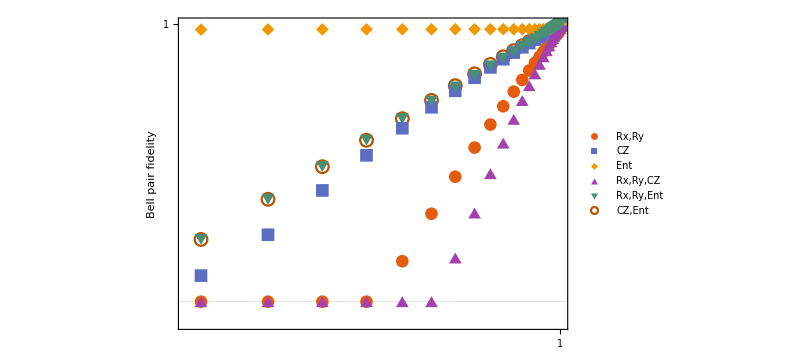

```mathematica
fplot1=ListLogLogPlot[#[[All,{1,3}]][[5;;]]&/@Values[fidvars],PlotRange->All,Frame->True,FrameStyle->Directive[Black,Thick],PlotMarkers->{Automatic, 13},BaseStyle->{17,FontFamily->"Sans Serif"},AspectRatio->0.6,PlotTheme->"Scientific",FrameLabel->{None,"Bell pair fidelity"},ImageSize->600,Joined->Join[ConstantArray[False,Length@fidvars],ConstantArray[True,Length@fidvars]],PlotStyle->Dashed,PlotLegends->Placed[LineLegend[{"Rx,Ry","CZ","Ent","Rx,Ry,CZ","Rx,Ry,Ent","CZ,Ent"},Spacings->0.,LegendFunction->(Framed[#,FrameStyle->(Antialiasing->False),FrameMargins->0,Background->White]&)],{0.89,0.2}],GridLines->{{},{0.95}},GridLinesStyle->{{{Thick,Red}},{}}]
```

```mathematica
(*Export["~/vqd/img/tions_vars.pdf",fplot1]*)
```

~/vqd/img/tions_vars.pdf

```mathematica
(*#->Transpose[{1-fidvars[#][[All,1]],(1-fidvars[#][[All,3]])}]&/@Keys[fidvars]*)
```

### Timing and time profiling on each operations

```mathematica
totaltime=Join[{1,Last[#[[1]][[All,1]]]}->#[[2]]&/@round1,
{2,Last[#[[1]][[All,1]]]}->#[[2]]&/@round2,
{3,Last[#[[1]][[All,1]]]}->#[[2]]&/@round3];
```

```mathematica
ListPlot[totaltime,Frame->True,PlotTheme->"Scientific",FrameLabel->{"distillation round","total time (μs)"},ScalingFunctions->"Log",FrameTicks->{{Automatic,Automatic},{{1,2,3},None}},FrameStyle->Directive[Black,Thick],BaseStyle->{13,FontFamily->"Sans Serif"},PlotMarkers->{"OpenMarkers", Small},ImageSize->330,AspectRatio->0.6]
(*Export["~/vqd/img/tions_totaltime.pdf",%]*)
```

-Graphics-

```mathematica
totaltime
```

{{1,61.}→raw,{1,462.73}→ph,{1,412.73}→bf,{2,1322.29}→ph,ph,{2,1272.29}→ph,bf,{2,1141.19}→bf,ph,{2,1091.19}→bf,bf,{3,2935.47}→ph,ph,ph,{3,2935.16}→ph,ph,bf,{3,2931.42}→ph,bf,ph,{3,2669.21}→bf,ph,ph,{3,2619.21}→bf,ph,bf,{3,2448.11}→bf,bf,ph,{3,2881.42}→ph,bf,bf,{3,2398.11}→bf,bf,bf}

```mathematica
opt=Options@TrappedIonOxford
```

{Nodes→<|Alice→4,Bob→4|>,T1→<|Alice→3000000000,Bob→3000000000|>,T2s→<|Alice→100000,Bob→100000|>,StdPassiveNoise→True,DurMove→<|Alice→<|Shutl→25,Splz→50,Comb→50,SWAPLoc→10|>,Bob→<|Shutl→25,Splz→50,Comb→50,SWAPLoc→10|>|>,FidInit→<|Alice→0.9999,Bob→0.9998|>,DurInit→<|Alice→20,Bob→20|>,DurRead→<|Alice→50,Bob→50|>,BFProb→<|Alice→1/1000,Bob→1/1000|>,ScatProb→<|Alice→0.05,Bob→0.05|>,FidSingleXY→<|Alice→0.99999,Bob→0.99999|>,EFSingleXY→<|Alice→{1,0},Bob→{1,0}|>,RabiFreq→<|Alice→10,Bob→10|>,FreqCZ→<|Alice→0.1,Bob→0.1|>,FidCZ→<|Alice→0.999,Bob→0.999|>,EFCZ→<|Alice→{0.1,0.9},Bob→{0.1,0.9}|>,FreqEnt→0.1,FidEnt→0.95,EFEnt→{0.1,0.9}}

```mathematica
SetAttributes[getTime,HoldAll]
getTime[gate_,lopt_]:=Module[{g,node,moves,sgate,θ,opt=Association[lopt]},
{g,node}=gate/.Subscript[gg_, __][n_,___]:>{gg,n};
moves={Splz,Comb,SWAPLoc,Shutl};
sgate={Rx,Ry};
Which[
MemberQ[moves,g],
opt[DurMove][node][g]
,
MemberQ[sgate,g],
θ=gate/.{Subscript[_, _][_,t_]:>t};
Abs[θ]/opt[RabiFreq][node]
,
g===CZ,
π/opt[FreqCZ][node]
,
g===Ent,
π/opt[FreqEnt],
g===Init,
opt[DurInit][node],
g===Read,
opt[DurRead][node],
True,
0
]
]
```

```mathematica
timeProfile[circ_,opt_,keys_:{}]:=Module[{time,gid,nodes,node,tkeys},
nodes=Keys[<|opt|>[Nodes]];
tkeys=If[Length@keys<1,DeleteDuplicates[circ/.Subscript[g_, __][n_,___]:>g],keys];
time=<|#->AssociationThread[tkeys->0]&/@nodes|>;
Table[
{gid,node}=gate/.Subscript[g_, __][n_,___]:>{g,n};
If[gid===Ent,
time[#][gid]+=getTime[gate,opt]&/@(gate/.Subscript[Ent, __][n1_,n2_]:>{n1,n2})
,
time[node][gid]+=getTime[gate,opt]
];
,{gate,circ}];
Association@Table[
n->KeyDrop[time[n],Wait],
{n,nodes}]
]
```

```mathematica
countProfile[circ_,opt_,keys_:{}]:=Module[{count,gid,nodes,node,tkeys},
nodes=Keys[<|opt|>[Nodes]];
tkeys=If[Length@keys<1,DeleteDuplicates[circ/.Subscript[g_, __][n_,___]:>g],keys];
count=<|#->AssociationThread[tkeys->0]&/@nodes|>;
Table[
{gid,node}=gate/.Subscript[g_, __][n_,___]:>{g,n};
If[gid===Ent,
count[#][gid]+=1&/@(gate/.Subscript[Ent, __][n1_,n2_]:>{n1,n2}),
count[node][gid]+=1
];
,{gate,circ}];
Association@Table[n->KeyDrop[count[n],Wait],{n,nodes}]
]
```

```mathematica
timeprofileplot[node_,data_,keys_,title_,legend_:True,opt_:{}]:=BarChart[data[[All,2]][[All,node]],ChartLabels->{Rotate[#,-π/3]&/@data[[All,1]],None},Sequence@@opt,
Frame->True,FrameStyle->Directive[Black,Thick],ChartLayout->"Percentile",ChartStyle->"ThermometerColors",ImageSize->330,BarSpacing->{1,0.3},BaseStyle->{12,FontFamily->"Times"},FrameLabel->{{None,None},{None,title}},If[legend,ChartLegends->Placed[keys,Right],Sequence@@{}],AspectRatio->1];
```

```mathematica
keys={Splz,Comb,Shutl,SWAPLoc,Ent,CZ,Ry,Rx,Read};
```

```mathematica
datatime={seqlabel[#],timeProfile[DistCircTrappedIons4[#],opt,keys]}&/@
{{},{0},{1},{0,0},{1,1},{0,0,0},{1,1,1}};
datacount={seqlabel[#],countProfile[DistCircTrappedIons4[#],opt,keys]}&/@
{{},{0},{1},{0,0},{1,1},{0,0,0},{1,1,1}};
plot1=timeprofileplot["Alice",datacount,keys,"Operation count(%)",False,{ImagePadding->{{20,0},{55,30}},ImageSize->220}];
plot2=timeprofileplot["Alice",datatime,keys,"Time spent on operations(%)",True,{ImagePadding->{{0,0},{55,30}},ImageSize->200}];
```

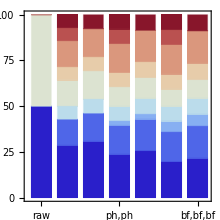
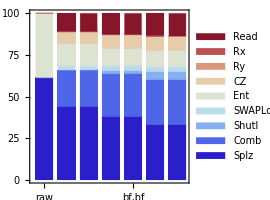
-Graphics- | -Graphics-

~/vqd/img/tions_timeprofile.pdf

```mathematica
Grid[{{plot1,plot2}},Spacings->0]
Export["~/vqd/img/tions_timeprofile.pdf",%]
```

## Print the step-by-step distillation process + animation

```mathematica
AnimateDistillation::usage="AnimateDistillation[sequence, device_options]";
AnimateDistillation[sequence_:{},devoptions_:{}]:=Module[
{dev,circ,ccirc,show={},format,noisy,fulltime,step=1,nions},
format[zones_,noise_,t_,s_]:=Framed[Row@{Column[{"("<>ToString[s]<>") t="<>ToString[t,TraditionalForm]<>"μs",Rasterize[zones,RasterSize->500,ImageSize->200]},Center],Pane[noise,280]}];
dev=TrappedIonOxford[Sequence@@devoptions];

nions=Min[Length/@Flatten/@Values@Values@dev[Nodes]];
circ=If[nions<=3,
DistCircTrappedIons3[sequence],
DistCircTrappedIons4[sequence]
];
ccirc=CircTrappedIons[circ,dev,MapQubits->False];
 fulltime=ToString[N@#,FormatType->TraditionalForm]&/@(InsertCircuitNoise[ccirc,TrappedIonOxford[Sequence@@devoptions]][[All,1]]+OptionValue[TrappedIonOxford,DurInit]["Alice"]);
AppendTo[show,format[dev[ShowNodes],DrawCircuit[{Subscript[Init, #]&/@Range[0,5],Subscript[Damp, #][1.]&/@Range[0,5]}],"0",step++]];
Table[
noisy=InsertCircuitNoise[ccirc[[c]],dev];
AppendTo[show,
format[dev[ShowNodes],DrawCircuit[Flatten@noisy[[All,2]],dev[NumTotalQubits]],fulltime[[c]],step++]
]
,{c,Length@ccirc}];
show
]
```

```mathematica
(* Print distillation step by step *)
PrintDistillation[sequence_:{},devoptions_:{}]:=Module[
{dev,circ,ccirc,show={},format,noisy,fulltime,step=0,nions},
format[zones_,c_,t_,s_]:={Column[{"("<>ToString[s,FormatType->TraditionalForm]<>")t="<>t<>"μs",StringRiffle[ToString[#,FormatType->TraditionalForm]&/@c]},Left],Rasterize[zones,RasterSize->Full,ImageSize->150]};
dev=TrappedIonOxford[Sequence@@devoptions];

nions=Min[Length/@Flatten/@Values@Values@dev[Nodes]];
circ=If[nions<=3,
DistCircTrappedIons3[sequence],
DistCircTrappedIons4[sequence]
];
ccirc=CircTrappedIons[circ,dev,MapQubits->False];fulltime=ToString[N[#],FormatType->TraditionalForm]&/@(InsertCircuitNoise[ccirc,TrappedIonOxford[Sequence@@devoptions]][[All,1]]+OptionValue[TrappedIonOxford,DurInit]["Alice"]);
AppendTo[show,format[dev[ShowNodes],{"Initialisation"},"0",step++]];
Table[
noisy=InsertCircuitNoise[ccirc[[c]],dev];
AppendTo[show,
format[dev[ShowNodes],ccirc[[c]],fulltime[[c]],step++]
]
,{c,Length@ccirc}];
show
]
```

```mathematica
(**   Render the steps into GIF animation   **)
(*picts = AnimateDistillation[{0,0,1}];
Export["distillation.gif", picts, AnimationRepetitions -> 1, "DisplayDurations" -> ConstantArray[1, Length@picts], RasterSize ->600];
Import["distillation.gif", "AnimatedImage"]*)
```

```mathematica
steps=PrintDistillation[{0,0,0}];
```

```mathematica
Length@steps
```

89

```mathematica
(*Export["~/vqd/img/distillation_steps1.pdf",TableForm@steps[[;;21]]]
Export["~/vqd/img/distillation_steps2.pdf",TableForm@steps[[22;;42]]]
Export["~/vqd/img/distillation_steps3.pdf",TableForm@steps[[43;;64]]]
Export["~/vqd/img/distillation_steps4.pdf",TableForm@steps[[65;;87]]]*)
```